```mathematica
Integrate[x^n / (a + x)^(k+1), {x,δ,∞}]
```

ConditionalExpression[(-a)^(-k+n) Beta[-a/δ,k-n,-k],Re[δ]>0&&δ==Re[δ]&&Re[a]>0&&Re[k]>Re[n]]

## (1) Bound (rough)

(∫_δ)^∞x^n/(x+a)^(k+1)ⅆx
= a^(-k+n) (∫_0)^(a/δ)t^(k-n-1)(1+t)^(-k-1)ⅆt

We use

t^(k-n-1) ≤ (a/δ)^(k-n-1).

```mathematica
(* k≥n+1 *)
bound = δ^(n+1)(δ^(-k)-(a+δ)^(-k)) / (a k)
kmin   = n+1
```

(δ^(1+n) (δ^-k-(a+δ)^-k))/(a k)

1+n

{(-1)^(2-k) Beta[-2,-2+k,-k],(-(2/3)^k+2^k)/(8 k)}

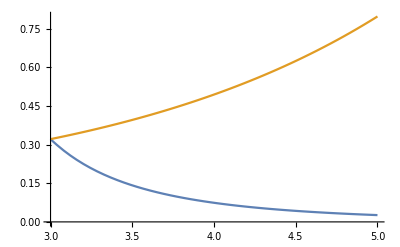

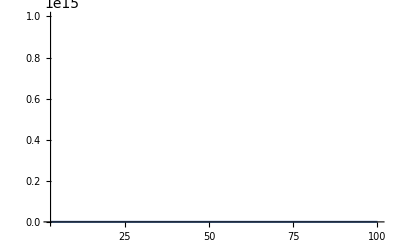

```mathematica
vals={δ->1/2,a->1,n->2};
{(-a)^(-k+n) Beta[-a/δ,k-n,-k], bound} /. vals
Plot[%, {k, kmin/.vals,kmin+2/.vals}]
Plot[%%, {k,kmin /.vals,100}]
```

## (2) Bound~O((a+δ)^-k)

(∫_δ)^∞x^n/(x+a)^(k+1)ⅆx
= a^(-k+n)(∫_0)^(a/δ)t^(k-n-1)(1+t)^(-k-1)ⅆt

Noting that

d/dt t^(k-n-1)(1+t)^(-k-1) ∝ (-n-2) (t-(k-n-1)/(n+2)),

the integrand is maximized at t=a/δ when (k-n-1)/(n+2)≥a/δ, and at t=(k-n-1)/(n+2) when 0<(k-n-1)/(n+2)≤a/δ.
We have the following upper bounds:

< δ^(n+1) (a+δ)^(-k-1)

for

(k-n-1)/(n+2)≥a/δ,

and

< a^(-k+n+1)δ^-1((k-n-1)/(n+2))^(k-n-1)((k+1)/(n+2))^(-k-1) ≤ δ^(-k+n)((k+1)/(n+2))^(-k-1)

for

0≤(k-n-1)/(n+2)≤a/δ.

{a→6,b→10}

3/2

{t^6/(1+t)^10,11664/9765625}

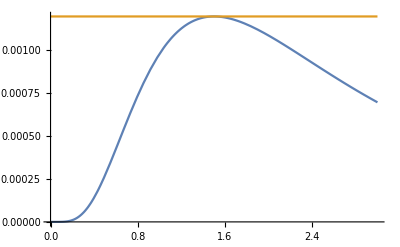

```mathematica
(* t^a(1+t)^-b *)
vals={a->6, b->10}
t0=-a/(a-b) /.vals
t^a (1+t)^(-b);
{%, %/.t->t0} /. vals
Plot[%, {t,0,2t0}]
```

```mathematica
(* (k-n-1)/(n+2) ≥ a/δ *)
bound1=δ^(n+1) (a+δ)^(-k-1)
kmin1 = (a/δ) (n+2) + n + 1
```

δ^(1+n) (a+δ)^(-1-k)

1+n+(a (2+n))/δ

```mathematica
(* 0 ≤ (k-n-1)/(n+2) ≤ a/δ *)
bound2 = a^(-k+n+1) δ^(-1) ((k-n-1)/(n+2))^(k-n-1) ((k+1)/(n+2))^(-k-1)
(*bound2 = δ^(-k+n) ((k+1)/(n+2))^(-k-1)*)
kmin2 = n+ 1
kmax2 = (a/δ) (n+2) + n + 1
```

(a^(1-k+n) ((1+k)/(2+n))^(-1-k) ((-1+k-n)/(2+n))^(-1+k-n))/δ

1+n

1+n+(a (2+n))/δ

### a+δ > 1

(k-n-1)/(n+2) ≥ a/δ

k ≥ 11

{(-1)^(2-k) Beta[-2,-2+k,-k],2^(-2+k) 3^(-1-k)}

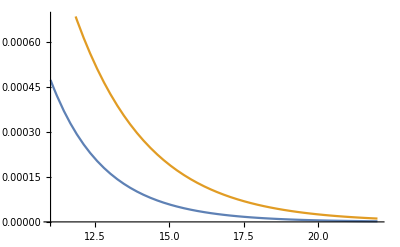

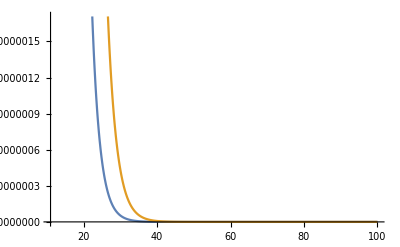

0 ≤ (k-n-1)/(n+2) ≤ a/δ

3 ≤ k ≤ 11

{(-1)^(2-k) Beta[-2,-2+k,-k],512 (-3+k)^(-3+k) (1+k)^(-1-k)}

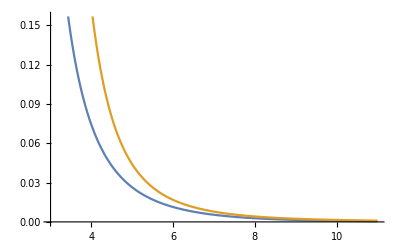

0 ≤ (k-n-1)/(n+2)

k ≥ 3

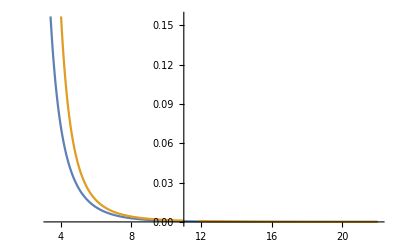

```mathematica
vals={δ->1/2,a->1,n->2};

Print[Style["(k-n-1)/(n+2) ≥ a/δ", Red]]
Print["k ≥ ",  (kmin1 /. vals)]
{(-a)^(-k+n) Beta[-a/δ,k-n,-k], bound1} /. vals
plt1=Plot[%, {k, kmin1/.vals,2kmin1/.vals}]
Plot[%%, {k,kmin1 /.vals,100}]

Print[Style["0 ≤ (k-n-1)/(n+2) ≤ a/δ", Red]]
Print[(kmin2/.vals), " ≤ k ≤ ", (kmax2 /. vals)]
{Normal[(-a)^(-k+n) Beta[-a/δ,k-n,-k]], bound2} /. vals
plt2=Plot[%, {k,kmin2 /.vals,kmax2 /. vals}]

Print[Style["0 ≤ (k-n-1)/(n+2)", Red]]
Print["k ≥ ",(kmin2/.vals)]
Show[plt1,plt2, PlotRange->Full]
```

### a+δ < 1

(k-n-1)/(n+2) ≥ a/δ

k ≥ 23/4

{(-1/4)^(5/2-k) Beta[-1/2,-5/2+k,-k],2^(-3/2+2 k) 3^(-1-k)}

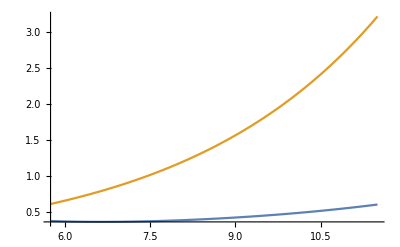

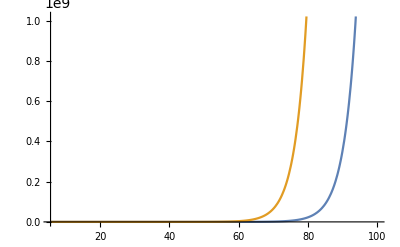

0 ≤ (k-n-1)/(n+2) ≤ a/δ

7/2 ≤ k ≤ 23/4

{(-1/4)^(5/2-k) Beta[-1/2,-5/2+k,-k],19683 2^(-21/2+2 k) (-7/2+k)^(-7/2+k) (1+k)^(-1-k)}

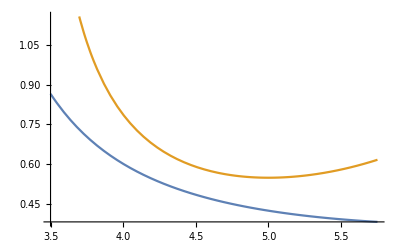

0 ≤ (k-n-1)/(n+2)

k ≥ 7/2

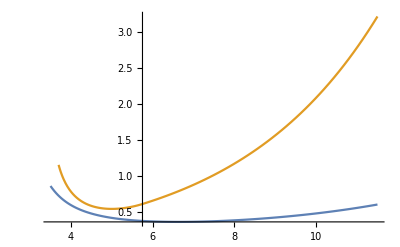

```mathematica
vals={δ->1/2,a->1/4,n->5/2};

Print[Style["(k-n-1)/(n+2) ≥ a/δ", Red]]
Print["k ≥ ",  (kmin1 /. vals)]
{(-a)^(-k+n) Beta[-a/δ,k-n,-k], bound1} /. vals
plt1=Plot[%, {k, kmin1/.vals,2kmin1/.vals}]
Plot[%%, {k,kmin1 /.vals,100}]

Print[Style["0 ≤ (k-n-1)/(n+2) ≤ a/δ", Red]]
Print[(kmin2/.vals), " ≤ k ≤ ", (kmax2 /. vals)]
{Normal[(-a)^(-k+n) Beta[-a/δ,k-n,-k]], bound2} /. vals
plt2=Plot[%, {k,kmin2 /.vals,kmax2 /. vals}]

Print[Style["0 ≤ (k-n-1)/(n+2)", Red]]
Print["k ≥ ", (kmin2/.vals)]
Show[plt1,plt2, PlotRange->Full]
```